# 1.1.4 2D Plotting Guide: Axes, Gridlines, Prologue, Epilogue

## Axes Options: Axes, Ticks, and Gridlines

```mathematica
f[x_]:=Sin[x^2]+x;
```

### Axes

In some contexts, we may want manipulate the axes by either removing an axis, labelling an axis, or changing the axis color. In the example below, we use Axes -> {True, False} to keep the x-axis but remove the y-axis. This axis is labelled using AxesLabel (and we would have labelled both axes if the y-axis was not removed), and AxesStyle specifies the x-axis to be orange and bold.

#### Example: Manipulating the axes with Axes, AxesLabel, and AxesStyle

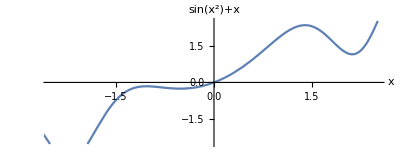

```mathematica
Plot[f[x],{x,-3,3},PlotRange->{{-2.5,2.5},{-2.5,2.5}},AspectRatio->2/5,Axes->{True,False},AxesLabel->{x,f[x]},AxesStyle->Directive[Orange,Bold]]
```

### Ticks

In a similar way to manipulating the axes, we may also want to manipulate the tally marks, or "ticks", along the axes. With Ticks ->{x-direction tally marks, y-direction tally marks}, we can do just that.

In the example below, we use the Table[ ] function to place a tally mark at .5 increments in the x-direction. We also specify the tally marks in the y-direction with the list {-2, 0, 2}.

#### Example: Manipulating the ticks with Ticks (and Table[ ])

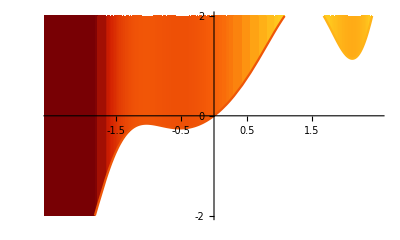

```mathematica
Plot[f[x],{x,-3,3},PlotRange->{{-2.5,2.5},{-2,2}},AspectRatio->3/5,ColorFunction->"SolarColors",Filling->Top, Ticks->{Table[.5+n,{n,-2,1,1}],{-2,0,2}}]
```

### Frame, GridLines, and GridLinesStyle

To frame your plot, just use Frame -> True. In a similar way to changing ticks, we can also add and manipulate the plot's grid with GridLines. In the example below, we add a frame, make it red with FrameStyle, and grid lines with GridLines-> Automatic.

#### Example: Adding a frame and grid lines

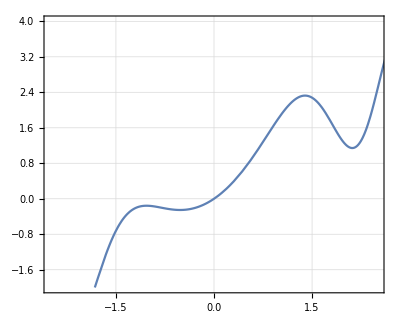

```mathematica
Plot[f[x],{x,-3,3},PlotRange->{{-2.5,2.5},{-2,4}},AspectRatio->4/5,Frame->True,FrameStyle->Red,GridLines->Automatic]
```

GridLinesStyle allows us to manipulate the grid lines style. In the example below, we add grid lines in .25 increments with Table[ ] in the x-direction and the y-direction. We also use GridLinesStyle to make the grid lines orange with small dashes.

#### Example: Manipulating GridLines with Table[ ] and GridLinesStyle

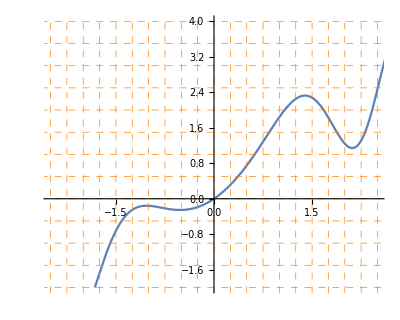

```mathematica
Plot[f[x],{x,-3,3},PlotRange->{{-2.5,2.5},{-2,4}},AspectRatio->4/5,GridLines->{Table[.25n,{n,-10,10}],Table[.5n,{n,-7,8}]},GridLinesStyle->Directive[Orange,Dashing[Small]]]
```

GridLines can be added in at specified places and with specified attributes. This is a particularly helpful way to highlight a point of emphasis on the plot. In the example below, we add grid lines in the x-direction at Pi/2 and 2 and in the y-direction at -1 and 2, each with a list of attributes.
Note: It is easy to miss a { or } when nestling lists. It is easiest, as always, to write outside-in. Start with GridLines ->{ }. Then add a list for the x-direction and y-direction grid lines respectively like GridLines -> { { }, { } }. Finally, make a list for each grid line added: GridLines -> { {{Pi/2,Red}, {2, Thick} }, { {-1, {Red, Thick}}, {2, Thick} } }.

#### Example: Specifying individual grid lines

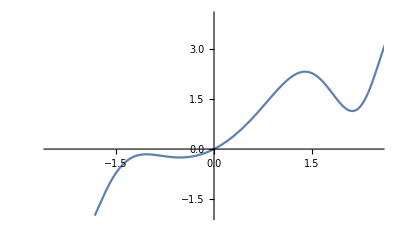

```mathematica
Plot[f[x],{x,-3,3},PlotRange->{{-2.5,2.5},{-2,4}},AspectRatio->3/5,GridLines->{{{Pi/2,{Red,Dashed}},{2,Thick}},{{-1,{Red,Thick,Dashed}},{2,Thick}}}]
```

## Additional Examples

#### Example: Plotting a function with its derivative with a number of specified attributes

In this example, we define h[x], and plot h[x] with its derivative h'[x].

```mathematica
h[x_]:=Cos[x^2]^3
```

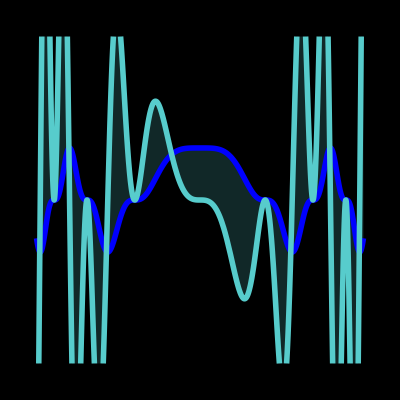

```mathematica
Plot[{h[x],h'[x]},{x,-Pi,Pi},PlotRange->{{-Pi,Pi},{-Pi,Pi}},AspectRatio->1,PlotStyle->{Directive[Blue,Thickness[0.01]],Directive[RGBColor[.34,.8,.8],Thickness[0.01]]},Background->Black,Axes->False,GridLines->{Table[Pi/4*n,{n,-4,4}],Table[Pi/4*n,{n,-12,12}]},GridLinesStyle->Directive[Orange,Dashed],Filling->{1->{2}}]
```

#### Example: Using Epilog

Epilog tells Mathematica to add a specified graphic (circles, rectangles, etc.) AFTER computing the initial plot. In this example, we use Epilog to insert a table of vertical lines through use of InfiniteLine[  ].

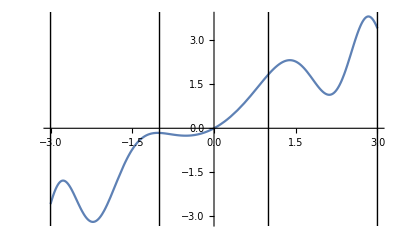

```mathematica
Plot[f[x],   {x, -3,3},  Epilog -> {Table[InfiniteLine[{2k+1,0},{0,1}],{k,-2,1}]}]
```

#### Example: Using Prolog to make a gradient background

Similarly to Epilog, Prolog tells Mathematica to add a specific graphic BEFORE computing the initial plot. In this example, we use Prolog to add a gradient background through Raster[  ].

```mathematica
r = Raster[   Table[i, {i, 100}, {j, 100}], {Scaled[{0, 0}], Scaled[{1, 1}]}, {1,
     100}, ColorFunction -> "DeepSeaColors"];
```

```mathematica
Plot[Evaluate[Table[f[x]+n, {n, -5,8}]],{x,-3,3},AspectRatio->1, PlotStyle-> Table[CMYKColor[.4k,.1k,.1k,.1k],{k,1,10}],Prolog->r ]
```

-Graphics-

If you wish to add gradient backgrounds, simply copy the Raster[ ] code above and change the name of the gradient to one of the gradients listed below.

```mathematica
ColorData["Gradients"]
```

{AlpineColors,Aquamarine,ArmyColors,AtlanticColors,AuroraColors,AvocadoColors,BeachColors,BlueGreenYellow,BrassTones,BrightBands,BrownCyanTones,CandyColors,CherryTones,CMYKColors,CoffeeTones,DarkBands,DarkRainbow,DarkTerrain,DeepSeaColors,FallColors,FruitPunchColors,FuchsiaTones,GrayTones,GrayYellowTones,GreenBrownTerrain,GreenPinkTones,IslandColors,LakeColors,LightTemperatureMap,LightTerrain,MintColors,NeonColors,Pastel,PearlColors,PigeonTones,PlumColors,Rainbow,RedBlueTones,RedGreenSplit,RoseColors,RustTones,SandyTerrain,SiennaTones,SolarColors,SouthwestColors,StarryNightColors,SunsetColors,TemperatureMap,ThermometerColors,ValentineTones,WatermelonColors}